```mathematica
flags = CountryData[#, "Flag"] & /@ CountryData[];
```

```mathematica
c = ImageCollage[1 -> flags, Automatic, 1000, 
  Background -> Transparent];
```

```mathematica
mask = AlphaChannel[c];
```

```mathematica
colors = DominantColors[c, Automatic, {"Coverage", "Color"}, 
  Masking -> mask]
```

{{0.239132,RGBColor[0.8225123458203405, 0.095538384313026, 0.16393540172050683, 0.9987180544797604]},{0.160869,RGBColor[0.9936581575475879, 0.9935790264845296, 0.9933338465593443, 0.998990821676482]},{0.10854,RGBColor[0.010237756056806376, 0.1424596599694206, 0.5272715012053502, 0.9987576278142313]},{0.0716423,RGBColor[0.9873910489369772, 0.8382730372232392, 0.08301700496512043, 0.9992111126191763]},{0.0643542,RGBColor[0.08432846800369825, 0.6063078565515314, 0.29040185939992763, 0.9974315879010938]},{0.0593235,RGBColor[0.05430721728459139, 0.4424212310179952, 0.2483152999088566, 0.9978178026474955]},{0.0554687,RGBColor[0.0990628111058636, 0.36400100530694196, 0.6840636978149015, 0.9986162127518072]},{0.044098,RGBColor[0.011558215541386047, 0.010438703049718006, 0.00819917956209669, 0.998280097003733]},{0.0411228,RGBColor[0.2703029691999983, 0.5797028582130597, 0.8514238190860512, 0.9985554609177769]},{0.0235077,RGBColor[0.6376238203218392, 0.13942645516754254, 0.21094004998539817, 0.9965092024389517]},{0.0113636,RGBColor[0.15474967165941528, 0.6618750950032624, 0.7868339486085165, 0.9981665394522927]},{0.00813695,RGBColor[0.9248650981255434, 0.4760565717809841, 0.0849690748295116, 0.9990924402803304]},{0.00258442,RGBColor[0.04804601145422321, 0.49683513760820536, 0.9913709909800462, 0.9993934198394313]}}

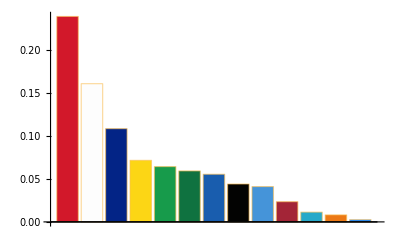

```mathematica
BarChart[colors[[All, 1]], ColorFunction -> (# /. Rule @@@ colors &), 
 ColorFunctionScaling -> False]
```

```mathematica
PieChart[colors[[All, 1]], ColorFunction -> (# /. Rule @@@ colors &), 
 ColorFunctionScaling -> False]
```

-Graphics-